```mathematica
Integrate[1/(a x + b),x]
```

Log[b+a x]/a

```mathematica
L:=1
Q:=L/15
c:=-2/((L-Q)(1/κu+1/κl)+2Q/(κu-κl)Log[κu/κl])
f[z_]:=1+c/κl(If[z>-Q,-Q,z]+L)+2 Q c/(κu-κl)Log[If[z>Q,κu/κl,If[z<-Q,1,(κu-κl)z/2/Q/κl+(κu+κl)/2/κl]]]+If[z>Q,c/κu*(z-Q),0]
```

```mathematica
Simplify[f[-Q]]
```

((κl-κu)^2-2 κl κu Log[κu/κl])/(κl^2-κu^2-2 κl κu Log[κu/κl])

```mathematica
Simplify[((κu-κl)(-Q)/2/Q+(κu+κl)/2)/κl]
```

1

```mathematica
κl:=1
κu:=100
```

```mathematica
c
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

Indeterminate

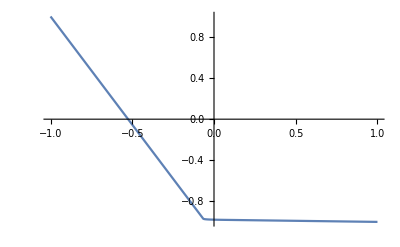

```mathematica
Plot[f[z],{z,-L,L}]
```

```mathematica
N[f[L]]
```

-1.